# Images for Probability for Calculus Students

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer

```mathematica
<<MaTeX`
```

### Figure 1: Decorative normal plot

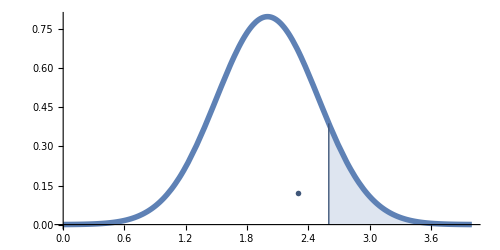

```mathematica
x0 = 2.6;
f[m_,s_][x_] = Exp[-(x-m)^2/(2 s^2)]/Sqrt[2Pi s^2];
p1 = Plot[f[2,1/2][x],{x,x0,4}, PlotStyle->{Thin},
Filling->Axis];
p2 = Plot[f[2,1/2][x],{x,0,4}, PlotStyle->{Thickness[0.008]}];
pic1 = Show[{p1,p2}, PlotRange -> All, AxesOrigin->{0,0},
Epilog -> {Darker[RGBColor[0.368417,0.506779,0.709798]], Line[{{x0,f[2,1/2][x0]},{x0,0}}],
Text[MaTeX["P\\approx"<>ToString[NIntegrate[f[2,1/2][x],{x,x0,Infinity}, WorkingPrecision->3]], FontSize -> 10],{2.3,0.12}]},
AspectRatio -> 1/2, ImageSize -> 500
]
```

```mathematica
Export[NotebookDirectory[]<>"Figure1.pdf",pic1]
Export[NotebookDirectory[]<>"Figure1.svg",pic1]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure1.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure1.svg

### Figure 2: Uniform distribution

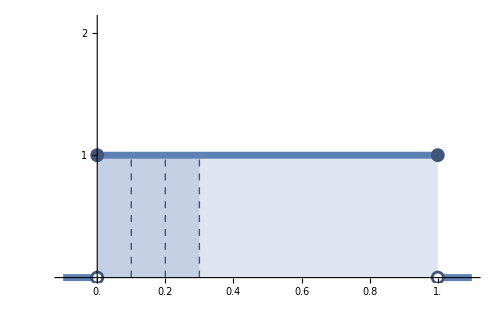

```mathematica
c = RGBColor[0.368417,0.506779,0.709798];
pic2 = Show[{
Plot[1, {x,0,1}, Filling->Axis, PlotStyle->Thin],
Plot[1, {x,0,0.3}, Filling->Axis, PlotStyle->Thin],
Plot[Piecewise[{{1,0<x<1},{0,True}}], {x,-0.1,1.1},
PlotRange->{{-0.1,1.1},{0,2.1}}, PlotStyle->Thickness[0.01]]
}, PlotRange->{{-0.1,1.1},{0,2.1}}, Ticks -> {Range[0,1,0.1],{1,2}},
Epilog -> {Dashed,Darker[c],Line[{ {{0.1,0},{0.1,1}}, {{0.2,0},{0.2,1}}, {{0.3,0},{0.3,1}} }],
PointSize[0.02],Point[{{0,1},{1,1},{0,0},{1,0}}],
White, PointSize[0.012], Point[{{0,0},{1,0}}]}, ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"Figure2.pdf",pic2]
Export[NotebookDirectory[]<>"Figure2.svg",pic2]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure2.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure2.svg

### Figure 3: Discrete distributions

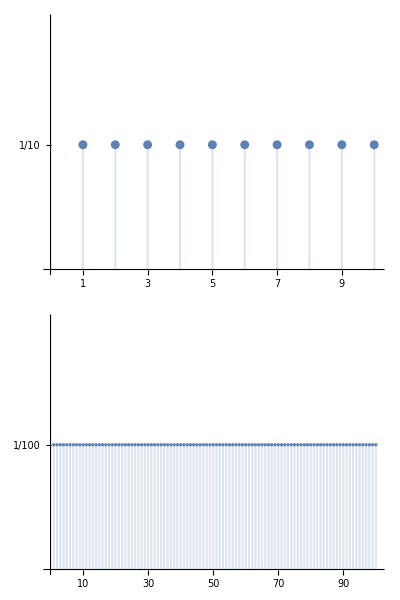

```mathematica
pic3= Grid[{
{DiscretePlot[1/10,{n,1,10}, ImageSize->500,
PlotRange->{{0,10.1},{0,0.2}},
Ticks -> {Range[1,10],{1/10}}]},
{DiscretePlot[1/100,{n,1,100}, ImageSize->500,
PlotRange->{{0,100.5},{0,0.02}},
Ticks -> {Range[10,100,10],{1/100}}]}
}]
```

```mathematica
Export[NotebookDirectory[]<>"Figure3.pdf",pic3]
Export[NotebookDirectory[]<>"Figure3.svg",pic3]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure3.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure3.svg

### Figure 4: Heads Tails

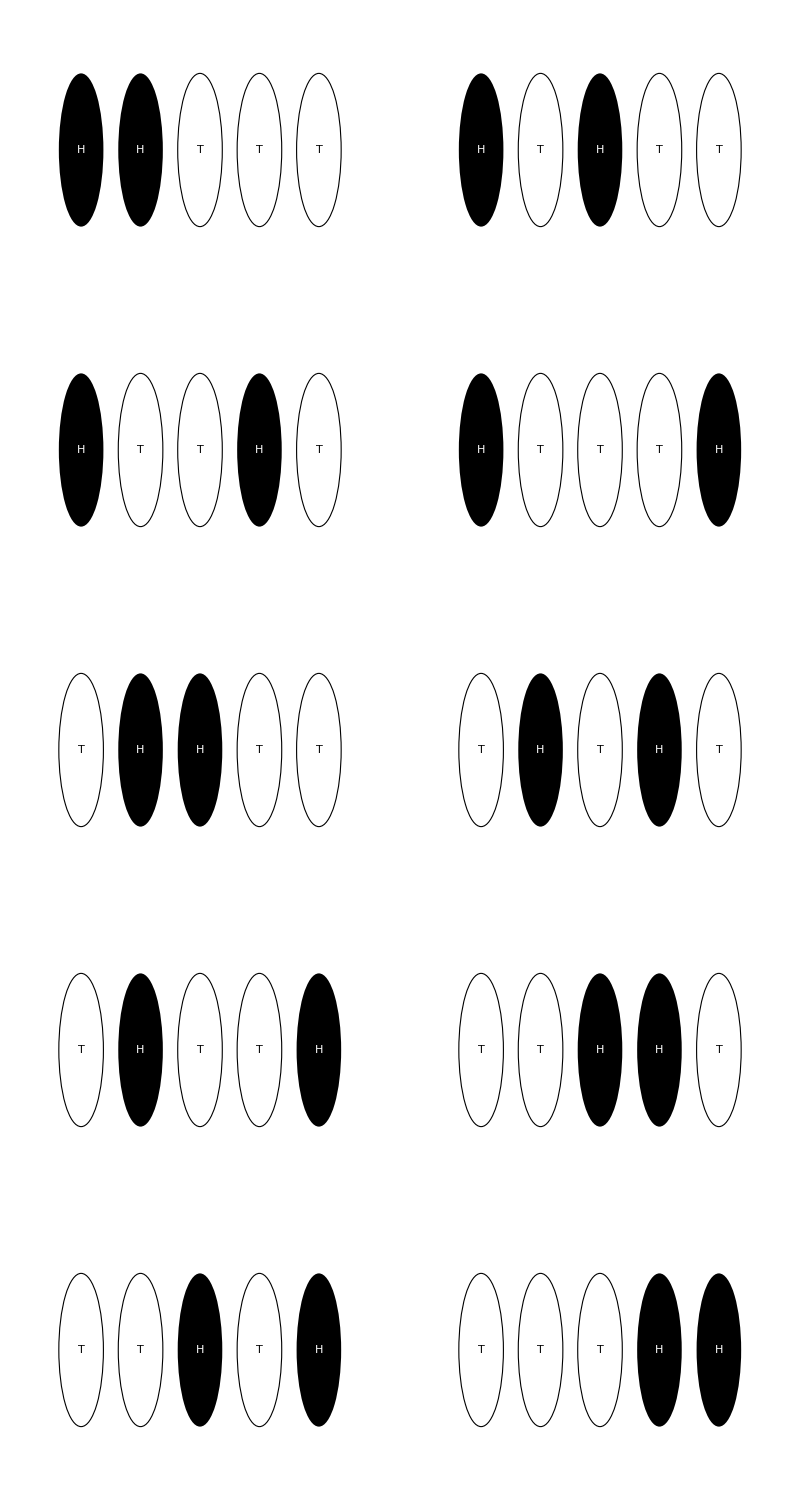

```mathematica
htPrimitive[ht_,{k_}] := If[ht==1, 
{Black, Disk[{2k,0},0.75],White,Style[Text["H",{2k,0}],FontSize -> 22]},
{EdgeForm[Black],White, Disk[{2k,0},0.75],Black,Style[Text["T",{2k,0}],FontSize -> 22]}];
htPic[tuple_] := Graphics[MapIndexed[htPrimitive,tuple], Frame->False,FrameStyle -> {Thick,Black},
 FrameTicks->False, ImageSize -> 250, PlotRange -> {{0.5,11.5},{-1.2,1.2}}]
pic4 = Grid[Partition[htPic /@ Reverse@Select[Tuples[{0,1},5],Total[#]==2&],2], Spacings->{0,0},Dividers->All,
Frame->True]
```

```mathematica
Export[NotebookDirectory[]<>"Figure4.pdf",pic4]
Export[NotebookDirectory[]<>"Figure4.svg",pic4]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure4.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure4.svg

### Figure 5: Binomial distribution plots

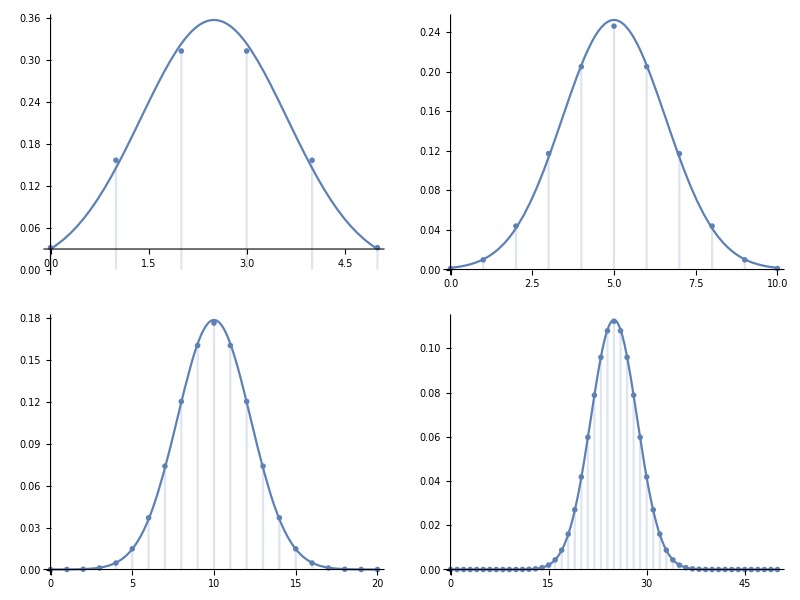

```mathematica
pic5 = Grid[Partition[Table[
m = n/2;
s = Sqrt[n]/2;
Show[{
Plot[Exp[-(x-m)^2/(2 s^2)]/Sqrt[2Pi*s^2],{x,0,n}, PlotRange -> All],
DiscretePlot[Binomial[n,k]/2^n,{k,0,n}, PlotMarkers->Style["·", FontSize -> 36]]
}, PlotRange -> All, ImageSize -> 250],
{n,{5,10,20,50}}], 2]]
```

```mathematica
Export[NotebookDirectory[]<>"Figure5.pdf",pic5]
Export[NotebookDirectory[]<>"Figure5.svg",pic5]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure5.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure5.svg

```mathematica
10/32.
```

```mathematica
0.3125
```

```mathematica
Sqrt[99]*8.
```

79.599

```mathematica
Sqrt[10^9]/2.
```

15811.4

### Figure 6: Basic pareto

```mathematica
Integrate[3/(1+x)^4,{x,0,Infinity}]
```

1

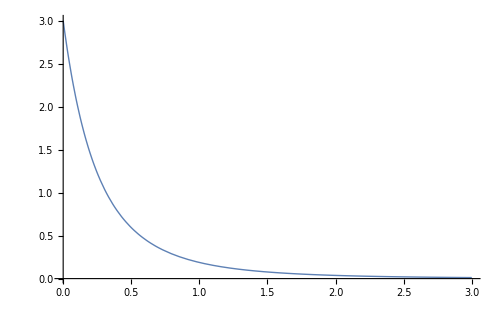

```mathematica
pic6 = Plot[3/(1+x)^4,{x,0,3}, PlotRange -> All, PlotStyle->Thick, ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"Figure6.pdf",pic6]
Export[NotebookDirectory[]<>"Figure6.svg",pic6]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure6.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure6.svg

### Figure 7 : Basic Pareto histogram

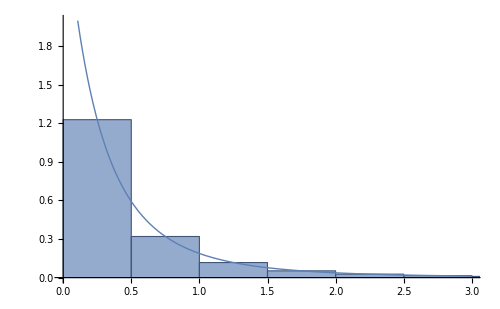

```mathematica
c = RGBColor[0.368417,0.506779,0.709798];
f[x_]= 3/(1+x)^4;
dx = 0.5;
pic7 = Plot[f[x],{x,0,3}, PlotRange -> {0,2}, PlotStyle->Thick,
Prolog->{EdgeForm[Darker[c]], Lighter[c], 
Table[Rectangle[{x,0},{x+dx,f[x+dx/2]}],{x,0,3,dx}]},
AxesOrigin->{0,0}, ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"Figure7.pdf",pic7]
Export[NotebookDirectory[]<>"Figure7.svg",pic7]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure7.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure7.svg

```mathematica
Integrate[x f[x],{x,0,Infinity}]
```

1/2

```mathematica
Integrate[(x-1/2)^2 f[x],{x,0,Infinity}]
```

3/4

```mathematica
Integrate[f[x],x]
```

-1/(1+x)^3

### Figure 8: Several normal plots

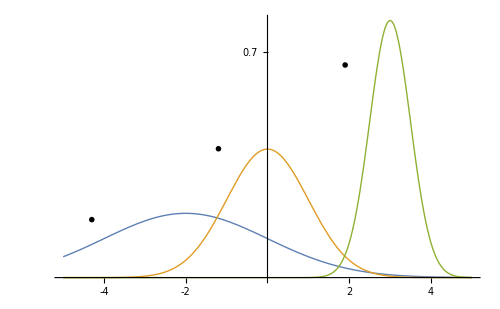

```mathematica
pic8 = Plot[{
f[-2,2][x],f[0,1][x],f[3,1/2][x]
},{x,-5,5}, PlotRange -> All, PlotStyle -> Thick, Epilog->{
Text[MaTeX["\\begin{array}{l}\\mu = -2 \\\\ \\sigma = 2 \\end{array}"],{-4.3,0.18}],
Text[MaTeX["\\begin{array}{l}\\mu = 0 \\\\ \\sigma = 1 \\end{array}"],{-1.2,0.4}],
Text[MaTeX["\\begin{array}{l}\\mu = 3 \\\\ \\sigma = 1/2 \\end{array}"],{1.9,0.66}]
}, Ticks -> {{-4,-2,2,4},{0.7}}, ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"Figure8.pdf",pic8]
Export[NotebookDirectory[]<>"Figure8.svg",pic8]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure8.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/Figure8.svg

### Fitting a Pareto distribution to ACS income data

We’re going to try to fit this generalized Pareto function:

```mathematica
Clear[m]
```

```mathematica
p[m_,a_,k_][x_] = (a/k)(k/(k+x-m))^(a+1)
```

(a (k/(-50000+k+x))^(1+a))/k

To the following ACS data on household incomes:

```mathematica
(* Households *)
cuttoffs = {0,10000,15000,25000,35000,50000,75000,100000,150000, 200000, 1000000};
binValues = {0.06,0.043,0.089,0.089,0.123,0.172,0.127,0.151,0.068, 0.077};
```

```mathematica
(* Individuals *)
cuttoffs = {0,10000,15000,25000,35000,50000,65000,75000,100000, 500000};
binValues = {0.016,0.028,0.116,0.156,0.196,0.157,0.061,0.112,0.158};
```

```mathematica
Total[binValues]
```

1.

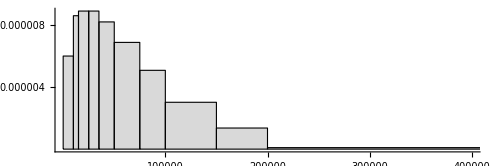

```mathematica
incomeHistogram = Graphics[
{EdgeForm[Black],LightGray,Table[
mm = cuttoffs[[i]];
h=binValues[[i]]/(cuttoffs[[i+1]]-mm);
Rectangle[{mm,0},{cuttoffs[[i+1]],h}],
{i,1,Length[binValues]}]}, AspectRatio->1/3,
PlotRange -> {{0,400000},All}, Axes->True,ImageSize->500,
Ticks->{100000*{1,2,3,4},{{0.000004,"0.000004"},{0.000008,"0.000008"}}}]
```

```mathematica
Export[NotebookDirectory[]<>"incomeHistogram.pdf",incomeHistogram]
Export[NotebookDirectory[]<>"incomeHistogram.svg",incomeHistogram]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/incomeHistogram.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/incomeHistogram.svg

Of course, the data tells us the proportions of households that we expect the distribution to predict for earning amounts between the cutoff values. For example, the proportion of households with earnings between $10000 and $15000 should be 0.043. Thus, we’ll try to minimize the mean squared error given by following objective function.

```mathematica
c = 6;
cuttoffs = cuttoffs[[c;;]]
binValues = binValues[[c;;]]/Total[binValues[[c;;]]]
```

{50000,75000,100000,150000,200000,1000000}

{0.289076,0.213445,0.253782,0.114286,0.129412}

```mathematica
Clear[m];
m = cuttoffs[[1]];
fit[m_?NumericQ,a_?NumericQ,k_?NumericQ] := Sum[
mm = If[i==1,m,cuttoffs[[i]]];
MM = If[i==Length[binValues],Infinity,cuttoffs[[i+1]]];
(NIntegrate[p[m,a,k][x],{x,mm,MM}] - binValues[[i]])^2,
{i,1,Length[binValues]}]
```

```mathematica
Clear[m];
fit[a_?NumericQ,k_?NumericQ] := Sum[
mm = cuttoffs[[i]];
MM = If[i==Length[binValues],Infinity,cuttoffs[[i+1]]];
(NIntegrate[p[m,a,k][x],{x,mm,MM}] - binValues[[i]])^2,
{i,1,Length[binValues]}]
```

```mathematica
{val,params} = FindMinimum[{fit[m,a,k], a>0&&k>0},{{a,4},{k,500000}}] // Quiet
```

{0.000685651,{a→8.65716,k→585742.}}

Let’s take a look:

```mathematica
p[m,a,k][x] /. params // TeXForm
```

7.40171\times 10^{50} \left(\frac{1}{x+535742.}\right)^{9.65716}

```mathematica
params
```

```mathematica
p[m,a,k][x]/.{a->8.657159926977723,k->585742.0713123148}
```

7.40171×10^50 (1/(535742.+x))^9.65716

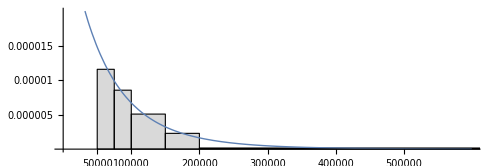

```mathematica
pic = Plot[p[m,a,k][x] /. params,{x,0,600000},
PlotRange -> {0,0.00002},PlotStyle -> Thick,
Prolog->{EdgeForm[Black],LightGray,Table[
mm = If[i==1,m/.params,cuttoffs[[i]]];
h=binValues[[i]]/(cuttoffs[[i+1]]-mm);
Rectangle[{mm,0},{cuttoffs[[i+1]],h}],
{i,1,Length[binValues]}]},AspectRatio->1/3,ImageSize->500,
Ticks -> {{50,100,200,300,400,500}*1000,{0.000015,0.00001,{0.000005,"0.000005"}}}]
```

```mathematica
Export[NotebookDirectory[]<>"pareto.pdf",pic]
Export[NotebookDirectory[]<>"pareto.svg",pic]
```

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/pareto.pdf

/Users/mcmcclur/Documents/html/classes/common/ProbabilityLaTeXed-newer/pareto.svg

```mathematica
Integrate[p[m,a,k][x] /. params,{x,100000,Infinity}]
```

0.492069

```mathematica
p[m,a,k][x] /. params // InputForm
```

7.401714313581143*^50*((535742.0713123148 + x)^(-1))^9.657159926977723

```mathematica
m
```

50000

```mathematica
mu = Integrate[x*p[m,a,k][x] /. params,{x,m,Infinity}]
```

126496.

```mathematica
std = Sqrt[Integrate[(x-mu)^2*p[m,a,k][x] /. params,{x,m,Infinity}]]
```

87233.2

```mathematica
Integrate[f[50m,Sqrt[50]std][x],{x,50*100000,Infinity}]
```

0.0000252861-2.01167×10^-15 ⅈ

```mathematica
f[mmm,sss][x]
```

(ⅇ^(-(-mmm+x)^2/(2 sss^2)))/(√(2 π) √(sss^2))

```mathematica
Integrate[p[m,a,k][x] /. params,{x,10^9,Infinity}]
```

7.5428×10^-20

```mathematica
g[m_,s_][x_] = Exp[-(x-m)^2/(2 s^2)]/Sqrt[2Pi s^2]
```

(ⅇ^(-(-m+x)^2/(2 s^2)))/(√(2 π) √(s^2))

```mathematica
Integrate[(x-m)^2*g[m,s][x],{x,-Infinity,Infinity}, Assumptions->{s>0,m>0}]
```

s^2

```mathematica
NIntegrate[g[mean,std][x],{x,5676.179642440387`22,Infinity}, WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (5.1385996372846670715×10^-6 ⅇ^(-8.29544019159237384×10^-11 (-«48»+x)^2)) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {24037.069584756933829}. NIntegrate obtained 0.70940774487960932214 and 0.37278651920140316177 for the integral and error estimates.

0.70940774487960932214

## Convert

```mathematica
SetDirectory[NotebookDirectory[]];
toConvert = FileNames["Figure*-eps-converted-to.pdf"]
```

{Figure1-eps-converted-to.pdf,Figure2-eps-converted-to.pdf,Figure3-eps-converted-to.pdf,Figure4-eps-converted-to.pdf,Figure5-eps-converted-to.pdf,Figure6-eps-converted-to.pdf,Figure7-eps-converted-to.pdf,Figure8-eps-converted-to.pdf,Figure9-eps-converted-to.pdf}

```mathematica
Do[
outputName = StringTake[file,7];
in = Import[file][[1]];
Export[outputName<>".pdf",in];
Export[outputName<>".svg",in],
{file,toConvert}]
```

```mathematica
StringTake["abc",2]
```

ab

```mathematica
Import["Figure2-eps-converted-to.pdf"][[1]]
```

```mathematica
Export["Figure2.svg",Import["Figure2-eps-converted-to.pdf"][[1]]]
```

Figure2.svg

```mathematica
Integrate[(a-1)/(1+x)^a,{x,0,Infinity},Assumptions->a>1]
```

1

```mathematica
(a-1)2^(a-1) /. a->4
```

24

```mathematica
1
```

```mathematica
Integrate[x(a-1)/(1+x)^a,{x,0,Infinity},Assumptions->a>2]
```

1/(-2+a)

```mathematica
Integrate[(x-1/(-2+a))^2(a-1)/(1+x)^a,{x,0,Infinity},Assumptions->a>3]//Simplify
```

(-1+a)/((-3+a) (-2+a)^2)

```mathematica
(-1+a)/((-3+a) (-2+a)^2)/. a -> 4
```

3/4

```mathematica
(4 (-1+a))/((-3+a) (-2+a)^2) /. a->12
```

11/225

```mathematica
Clear[m]
```

```mathematica
p[m,a,k][x]
```

(a (k/(k-m+x))^(1+a))/k

```mathematica
p[0,3,1][x]
```

3/(1+x)^4

```mathematica
f[m_,s_][x_] = Exp[-(x-m)^2/(2 s^2)]/Sqrt[2Pi s^2];
NIntegrate[f[98.2,0.62][x],{x,99.4,Infinity}]
```

0.0264655

```mathematica
F[a_?NumericQ] := NIntegrate[f[98.2,0.62][x],{x,a,Infinity}]
```

```mathematica
F[99]
```

0.0984693

```mathematica
FindRoot[F[a]==0.005,{a,99}]
```

{a→99.797}

```mathematica
F[99.7970141682005]
```

0.005

```mathematica
Integrate[f[98.2,0.62][x],{x,a,Infinity}]
```

0.+0. ⅈ

```mathematica
a
```

a

```mathematica
m = 98.2;
s = 0.62;
```

```mathematica
Sum[k*Binomial[27,k],{k,0,27}]/2^27
```

27/2

```mathematica
0.82*1290
```

1057.8

```mathematica
0.82*0.18*1290 // Sqrt
```

13.7987

```mathematica
p = 1/4;
n = 26;
m = n*p;
s = Sqrt[n*p*(1-p)];
NIntegrate[f[m,s][x],{x,10.5,Infinity}]
```

0.0350207

```mathematica
Sum[Binomial[n,k]*p^k(1-p)^(n-k),{k,11,n}] // N
```

0.0400845

```mathematica
NIntegrate[Exp[-(x-40)^2/80],{x,41.5,Infinity}]/Sqrt[80Pi]
```

0.406262

```mathematica
Sum[Binomial[80,k],{k,42,80}]/2^80//N
```

0.368777

```mathematica
/
```

```mathematica
Integrate[Sin[Pi*x],{x,1,2}]//N
```

-0.63662

```mathematica
1*1/2 + 2*1/4 + 4*1/4
```

2

```mathematica
(1-2)^2 1/2 + (2-2)^2 1/4 + (4-2)^2 1/4
```

3/2

```mathematica
m = 1/2 * 1 + 1/3 * 2 + 1/6 * 3
```

5/3

```mathematica
1/2 * (1-m)^2 + 1/3 * (2-m)^2 + 1/6 * (3-m)^2
```

5/9

```mathematica
Clear[m,s]
```

```mathematica
f[70,10][x]
```

(ⅇ^(-1/200 (-70+x)^2))/(10 √(2 π))